8

{{35,65,0,0,0,0,0,0,0,0,0,0},{23,11,28,37,0,0,0,0,0,0,0,0},{14,15,5,20,13,32,0,0,0,0,0,0},{9,14,7,4,15,13,11,27,0,0,0,0},{7,10,10,4,3,11,13,7,11,23,0,0},{6,8,10,6,2,3,9,12,8,6,12,20}}

{100,99,99,100,99,102}

0.0268493 (2+Cos[t]+Sin[t]+t Sin[t]^2+Sin[t]^8)

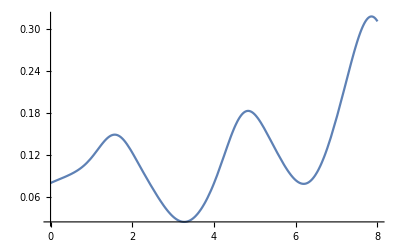

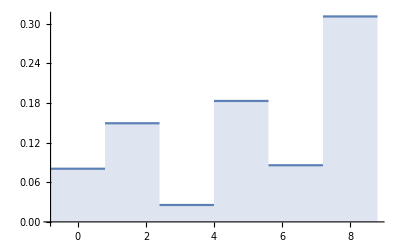

```mathematica
T=RandomInteger[{1,20}]
stake =100;
f[x_] = (x*Sin[x]^2+D[Cos[x],{x,T}]+D[Sin[x],{x,T}]+Sin[x]^T+2);
F[x_] = f[t]/NIntegrate[f[t],{t,0,T}];
S = Table[Table[Round[stake*NIntegrate[F[t],{t,i*T/rounds,(i+1)*T/rounds}]],{i,0,rounds-1}],{rounds,2,12,2}];
padS = Table[PadRight[Part[S,i],12],{i,1,6}]
check=Table[Sum[Part[padS,i,j],{j,1,Length[Part[S,i]]}],{i,1,6}]
F[x]
Plot[F[t],{t,0,T},PlotRange->Full ]
DiscretePlot[F[t],{t,0,T, T/(6-1)},ExtentSize->Full,ExtentMarkers->None]
```